# The New Seeker

Brian Beckman
9 Aug 2019

## Sampling

## Uniform in d-Ball—2 [ n, d ]

### Uniform in d-Ball: Slow

Probably because of the d×d matrix. Avoid.

```mathematica
ClearAll[uniformInBall];
uniformInBall[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
MultinormalDistribution[
IdentityMatrix[d+2]],n];
```

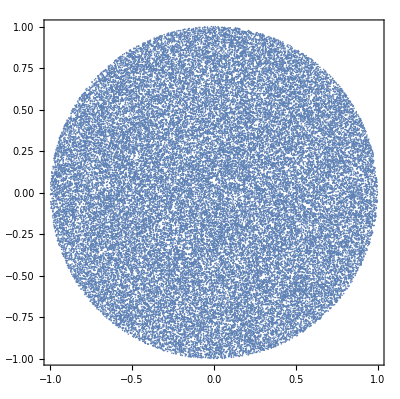

```mathematica
ListPlot[uniformInBall[],AspectRatio->Automatic,Frame->True]
```

### Uniform in d-Ball—2: Fast

```mathematica
ClearAll[uniformInBall2];
uniformInBall2[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
NormalDistribution[],{n,d+2}];
```

```mathematica
uniformInBall2[1,4]
```

{{0.0764491,-0.207016,-0.108596,-0.136951}}

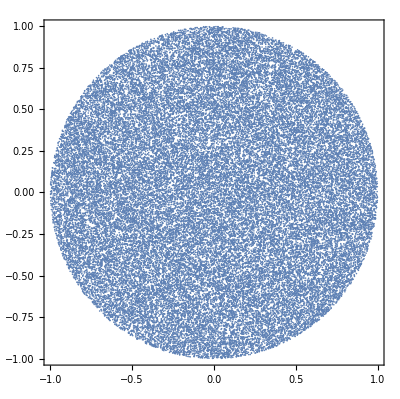

```mathematica
ListPlot[uniformInBall2[],AspectRatio->Automatic,Frame->True]
```

```mathematica
Timing[uniformInBall[1000,600];]
```

{2.73764,Null}

```mathematica
Timing[uniformInBall2[1000,6000];]
```

{0.629219,Null}

## Normal

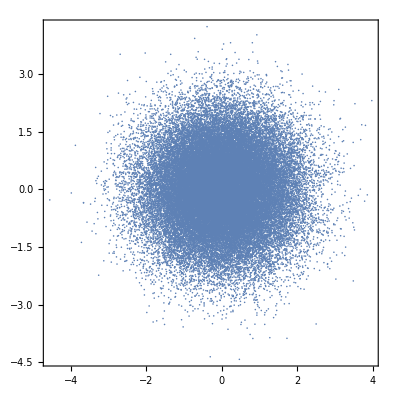

```mathematica
ListPlot[
RandomVariate[NormalDistribution[],{50000,2}],
AspectRatio->Automatic,Frame->True]
```

## Seeking

## Imperative Style (DEPRECATED)

```mathematica
ClearAll[sampleAB];
sampleAB[μ_,σ_,target_]:=
With[{
a=RandomVariate[NormalDistribution[#,σ]]&/@target,
b=RandomVariate[NormalDistribution[#,σ]]&/@target},
With[{
da=EuclideanDistance[a,target],
db=EuclideanDistance[b,target]},
If[da<db,{a,da},{b,db}]]];
```

```mathematica
ClearAll[getTarget];
getTarget[d_:4]:=uniformInBall2[1,d]⟦1⟧;
getTarget[4]
```

{0.0602333,0.739729,-0.0964152,0.239358}

```mathematica
ClearAll[DBALLRADIUS,echo,short,filter,experiment];
DBALLRADIUS=1.0;
echo=Identity;
short=Short;
experiment[d_,rollouts_:10,maxSamples_:10000,
allowedError_:0.1,decay_:0.992]:=
Module[{
averageTrialsPerSuccess=0,
percentageSuccessful=0,
result=Null,
convergeFailures=0,
convergeSuccesses=0,
convergeTotalTrials=0,
targets=ConstantArray[0,rollouts],
yps=ConstantArray[Null,rollouts],
distances=ConstantArray[0,rollouts],
convergeStepsS=ConstantArray[0,rollouts],
convergeSigmas=ConstantArray[0,rollouts],
convergeDistances=ConstantArray[0,rollouts],
convergeMaxDistances=ConstantArray[0,rollouts],
successP=ConstantArray[False,rollouts],
totalBigDist=0,
totalSmlDist=0,
dimDist=DBALLRADIUS,
covariance0=DBALLRADIUS^2,
covariance=0},
Do[    With[    {seekTarget=getTarget[d]},
Module[{count=0,    yp=ConstantArray[0,d],
distance=0,    maxDist=-1000000,    calcDistance=0},
covariance=covariance0;
While[    Module[{},
distance=EuclideanDistance[seekTarget,yp];
And[distance>allowedError,count<maxSamples]],
{yp,calcDistance}=echo@sampleAB[yp,Sqrt[covariance],seekTarget];
count+=1;
covariance*=decay;
If[    calcDistance<DBALLRADIUS,totalSmlDist+=1,
(*else*)    totalBigDist+=1];
maxDist=Max[maxDist,calcDistance]    ];
If[count<maxSamples,
Module[{},successP⟦rollout⟧=True;
convergeSuccesses+=1;
convergeTotalTrials+=count;    ],
Module[{},convergeFailures+=1;    ]];
targets⟦rollout⟧=seekTarget;
yps⟦rollout⟧=yp;
distances⟦rollout⟧=distance;
convergeStepsS⟦rollout⟧=count;
convergeSigmas⟦rollout⟧=Sqrt[covariance];
convergeDistances⟦rollout⟧=calcDistance;
convergeMaxDistances⟦rollout⟧=maxDist;    ]],
{rollout,rollouts}    ];
averageTrialsPerSuccess=
N@If[convergeSuccesses>0,convergeTotalTrials/convergeSuccesses,0];
percentageSuccessful=100.0*(rollouts-convergeFailures)/rollouts;
result=<|
"rollouts"->rollouts,
"failures"->convergeFailures,
"successes"->convergeSuccesses,
"targets"->targets,
"yps"->yps,
"spotCheckDistance"->EuclideanDistance[targets⟦1⟧,yps⟦1⟧],
"firstDistance"->distances⟦1⟧,
"distances"->distances,
"meanTrialsPerSuccess"->averageTrialsPerSuccess,
"percentageSuccessful"->percentageSuccessful,
"bigDistanceCount"->totalBigDist,
"smallDistanceCount"->totalSmlDist,
"originalSigma"->Sqrt[covariance0],
"covarianceDecay"->decay,
"convergeStepsS"->convergeStepsS,
"convergeSigmas"->convergeSigmas,
"convergeDistances"->convergeDistances,
"convergeMaxDistances"->convergeMaxDistances,
"successFlags"->successP
|>;
result    ];
filter[fullResult_]:=
With[{avg="meanTrialsPerSuccess",pct="percentageSuccessful",dec="covarianceDecay"},
<|avg->fullResult[avg],pct->fullResult[pct],dec->fullResult[dec]|>];
```

```mathematica
filter@experiment[4,100,10000,.1,.992]
```

<|meanTrialsPerSuccess→369.86,percentageSuccessful→100.,covarianceDecay→0.992|>

```mathematica
filter@experiment[4,100,10000.,.1,#]&/@Range[.900,.990,.010]
```

{<|meanTrialsPerSuccess→42.18,percentageSuccessful→100.,covarianceDecay→0.9|>,<|meanTrialsPerSuccess→45.62,percentageSuccessful→100.,covarianceDecay→0.91|>,<|meanTrialsPerSuccess→51.38,percentageSuccessful→100.,covarianceDecay→0.92|>,<|meanTrialsPerSuccess→58.05,percentageSuccessful→100.,covarianceDecay→0.93|>,<|meanTrialsPerSuccess→63.07,percentageSuccessful→100.,covarianceDecay→0.94|>,<|meanTrialsPerSuccess→80.3,percentageSuccessful→100.,covarianceDecay→0.95|>,<|meanTrialsPerSuccess→94.2,percentageSuccessful→100.,covarianceDecay→0.96|>,<|meanTrialsPerSuccess→120.43,percentageSuccessful→100.,covarianceDecay→0.97|>,<|meanTrialsPerSuccess→168.6,percentageSuccessful→100.,covarianceDecay→0.98|>,<|meanTrialsPerSuccess→306.34,percentageSuccessful→100.,covarianceDecay→0.99|>}

## Functional Style

### Visualization For Vetting the Algorithm

```mathematica
ClearAll[prtSeek2D,vizSeek2D,nexter,echo];
nexter[{yp_,dist_,A_,DA_,B_,DB_,cov_,j_},{t_,decay_,i_}]:=
Module[{σ=Sqrt[cov],a,b,da,db},
a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
da=EuclideanDistance[t,a];
db=EuclideanDistance[t,b];
With[{νcov=Quiet[cov*decay]},
If[da<db,
{a,da,a,da,b,db,νcov,i},
{b,db,a,da,b,db,νcov,i}]]];
ClearAll[picker,dist,yp,a,b,da,db,cov,i];
picker[n_]:=#⟦n⟧&;{yp,dist,a,da,b,db,cov,i}=picker/@Range[8];
echo=Echo;
vizSeek2D[tol_:0.1,dec_:0.992,maxIt_:10000,pr_:10,dim_:2]:=
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{decimator={indexer[yp[#]],dist[#],indexer[a[#]],da[#],indexer[b[#]],db[#],cov[#],i[#]}&},
With[{big=100,tar=getTarget[dim],cov0=DBALLRADIUS^2,ini=ConstantArray[0,dim]},
With[{all=FoldList[nexter,{ini,big,ini,big,ini,big,cov0,0},Table[{tar,dec,i},{i,maxIt}]]},
With[{surv=TakeWhile[all,(*True&*)(dist[#]>tol)&]},
With[{sampled=decimator/@surv,lsurv=Length[surv]},
Show[Graphics[{LightGray,Disk[],White,Disk[indexer@tar,0.3],Black,Circle[indexer@tar,0.3],
{Hue[(2.+i[#]*4/lsurv)/6.],Circle[yp[#],Sqrt[cov[#]]],Point[yp[#]]}&/@sampled,
Text[Style[lsurv,"Text",Background->White],{-pr/2,pr*0.90}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]]];
Manipulate[
vizSeek2D[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-σ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,2,"log_10(reps)"},0,5,0.25,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

### Convergence Statistics

```mathematica
ClearAll[repsTillConvergenceVsSigma,repsStatsTillConvergenceVsSigma,trial,episode];
With[{big=100,cov0=DBALLRADIUS^2},
trial[tar_,ini_,σ_,dim_:2,tol_:0.01,maxIt_:100000]:=
With[{all=
FoldList[nexter,
{ini,big,ini,big,ini,big,cov0,0},
Table[{tar,σ,i},{i,maxIt}]]},
With[{surv=TakeWhile[all,(dist[#]>tol)&]},
Length[surv]]]];
episode[tar_,ini_,σ_,dim_:2,tol_:0.01,maxIt_:100000,n_:10]:=
Map[trial[getTarget[dim],ini,σ,dim,tol,maxIt]&,Range[n]];
repsStatsTillConvergenceVsSigma[dim_:2,tol_:0.01,maxIt_:100000,n_:10]:=
With[{ini=ConstantArray[0,dim],
σs=Echo@Table[1-10.^-ld,{ld,.5,5.,0.25}]},
With[{lenss=N@ParallelMap[
episode[getTarget[dim],ini,#,dim,tol,maxIt,n]&,σs]},
{σs,Mean[lenss],StandardDeviation[lenss]}ᵀ]];
repsTillConvergenceVsSigma[dim_:2,tol_:0.01,maxIt_:100000]:=
With[{ini=ConstantArray[0,dim],
σs=Echo@Table[1-10.^-ld,{ld,.5,5.,0.25}]},
With[{lens=
ParallelMap[
trial[getTarget[dim],ini,#,dim,tol,maxIt]&,
σs]},
{σs,lens}ᵀ]];
(*episode[getTarget[2],ConstantArray[0,2],.99,2,0.01,100000]*)
(*repsTillConvergenceVsSigma[2,0.01,100000]//MatrixForm*)
repsStatsTillConvergenceVsSigma[2,0.01,100000,10]//MatrixForm
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

Transpose::nmtx: The first two levels of {{0.683772,0.822172,0.9,0.943766,«11»,0.999944,0.999968,0.999982,0.99999},«1»,{«1»}} cannot be transposed.

Transpose[{{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999},{14212.3,3119.21,10001.6,14138.7,16064.3,8662.53,3384.21,4399.89,5651.37,15861.2},{30581.8,4323.3,23748.4,30653.,30815.9,22632.,4989.72,7568.53,8568.62,30680.4}}]

```mathematica
repsTillConvergenceVsSigma[100,0.01,100000]//MatrixForm
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

(0.683772 | 100001
0.822172 | 100001
0.9 | 100001
0.943766 | 100001
0.968377 | 100001
0.982217 | 100001
0.99 | 100001
0.994377 | 100001
0.996838 | 6150
0.998222 | 10431
0.999 | 18053
0.999438 | 32032
0.999684 | 56185
0.999822 | 100001
0.9999 | 100001
0.999944 | 100001
0.999968 | 100001
0.999982 | 100001
0.99999 | 100001)

```mathematica
repsTillConvergenceVsSigma[1000,0.01,100000]//MatrixForm
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

(0.683772 | 100001
0.822172 | 100001
0.9 | 100001
0.943766 | 100001
0.968377 | 100001
0.982217 | 100001
0.99 | 100001
0.994377 | 100001
0.996838 | 100001
0.998222 | 100001
0.999 | 100001
0.999438 | 100001
0.999684 | 76399
0.999822 | 100001
0.9999 | 100001
0.999944 | 100001
0.999968 | 100001
0.999982 | 100001
0.99999 | 100001)

```mathematica
With[{dim=2000},
trial[getTarget[dim],ConstantArray[0,dim],0.999,dim,0.01,2000000]]
```

1000001

```mathematica
(*repsTillConvergenceVsSigma[6000,0.01,1000000]//MatrixForm*)
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,8234,12].

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {524} assigned to KernelObject[3,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[3,local,<defunct>] resurrected as KernelObject[7,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,8235,13].

Kernels::rdead: Subkernel connected through KernelObject[4,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {523} assigned to KernelObject[4,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[4,local,<defunct>] resurrected as KernelObject[8,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,8233,11].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {525} assigned to KernelObject[2,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[9,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

$Aborted